```mathematica
Ent[x_] := -x Log[2,x] - (1-x) Log[2, (1-x)]
```

```mathematica
Ent[.5]
```

1.

```mathematica
z[eps_] := 1/(2 + Sqrt[(1 - eps)/(1 + eps)])
```

```mathematica
z[1]
```

1/2

```mathematica
F[eps_] := (1/2) (1 - eps) 2^Ent[z[eps]] ((1+eps)/(1 - eps))^z[eps] 2^(Ent[z[eps]/(1 - z[eps])] (1 - z[eps]))
```

```mathematica
F[eps]
```

1/2 ⅇ^(-Log[1/(2+√((1-eps)/(1+eps)))]/(2+√((1-eps)/(1+eps)))-(1-1/(2+√((1-eps)/(1+eps)))) Log[1-1/(2+√((1-eps)/(1+eps)))]+(1-1/(2+√((1-eps)/(1+eps)))) Log[2] (-Log[1/((2+√((1-eps)/(1+eps))) (1-1/(2+√((1-eps)/(1+eps)))))]/((2+√((1-eps)/(1+eps))) (1-1/(2+√((1-eps)/(1+eps)))) Log[2])-((1-1/((2+√((1-eps)/(1+eps))) (1-1/(2+√((1-eps)/(1+eps)))))) Log[1-1/((2+√((1-eps)/(1+eps))) (1-1/(2+√((1-eps)/(1+eps)))))])/Log[2])) (1-eps) ((1+eps)/(1-eps))^(1/(2+√((1-eps)/(1+eps))))

```mathematica
F[.2]
```

1.3798

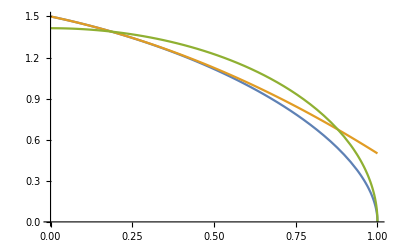

```mathematica
Plot[{F[x],3/2 - x/2 -x^2/2,Sqrt[2(1 + x)(1-x)]}, {x, 0, 1}]
```

```mathematica
F[.99999]
```

0.00447712

```mathematica
F[.6]
```

1.

```mathematica
G[eps_] := (1-eps)(1/2)2^Ent[z[eps]] ((1 + eps)/(1 - eps))^(z[eps]) 2^(1 - z[eps])
```

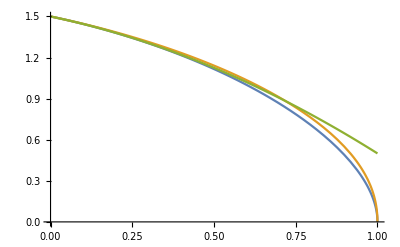

```mathematica
Plot[{F[x],G[x],3/2-x/2-x^2/2}, {x, 0, 1}]
```

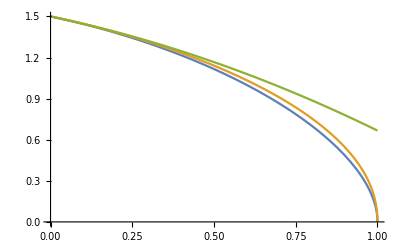

```mathematica
Show[%58,ImageSize->Full]
```

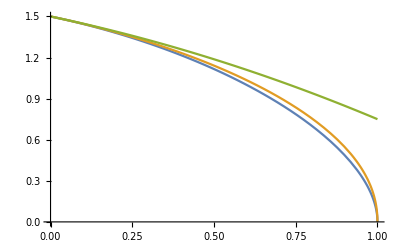

```mathematica
Show[%56,ImageSize->Full]
```